```mathematica
Get["C:\\Users\\Joan\\Google Drive\\Borsa\\Borsa mat\\Dades stocks\\TrendDetectStocks.mc"];
```

```mathematica
stocks
```

{MC:ABE,MC:ACS,MC:BBVA,MC:FCC,MC:GAS,MC:ELE,MC:SAN,MC:REP,MC:TEF,MC:GAM}

```mathematica
cs=FDClose[s[[1]]][[;;3800,2]];
```

```mathematica
sp60=kNNForecast[cs,20,1000,1];
```

```mathematica
Length[sp60]
```

3221

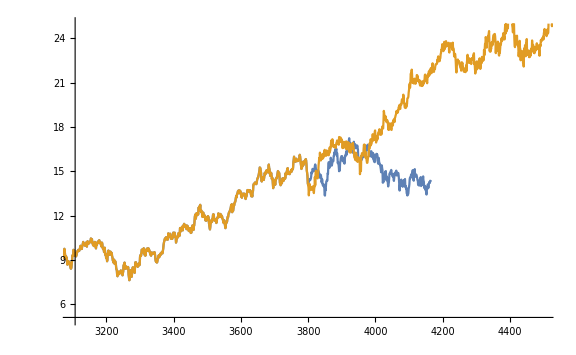

```mathematica
ListLinePlot[{FDClose[s[[1]]][[All,2]],sp60},PlotRange->{{3100,4500},{5,25}}]
```

```mathematica
csf=MPForecast[cs,20,120,Method->{"NeuralNetwork","L2Regularization"->0.01,"HiddenLayers"->{4,4,4}}];
```

Column::argb: Column called with 6 arguments; between 1 and 3 arguments are expected.

Predictor information
Method | Neural network
Number of features | 19
Number of training examples | 2981
L1 regularization coefficient | 0
L2 regularization coefficient | 
Number of hidden layers | 3
Hidden nodes | ,,444
Hidden layer activation functions | ,,TanhTanhTanh
CostFunction | Cost Function

```mathematica
csf=MPForecast[cs,20,120,Method->{"NearestNeighbors"}];
```

Column::argb: Column called with 6 arguments; between 1 and 3 arguments are expected.

Predictor information
Method | K-nearest neighbors
Number of features | 19
Number of training examples | 2981
Number of neighbors | 5
Distance function | EuclideanDistance

```mathematica
csf=MPForecast[cs,20,120,Method->{"RandomForest"}];
```

Column::argb: Column called with 6 arguments; between 1 and 3 arguments are expected.

Predictor information
Method | Random forest
Number of features | 19
Number of training examples | 2981
Number of trees | 50

```mathematica
csf=MPForecast[cs,20,120,Method->"GaussianProcess"];
```

$Aborted

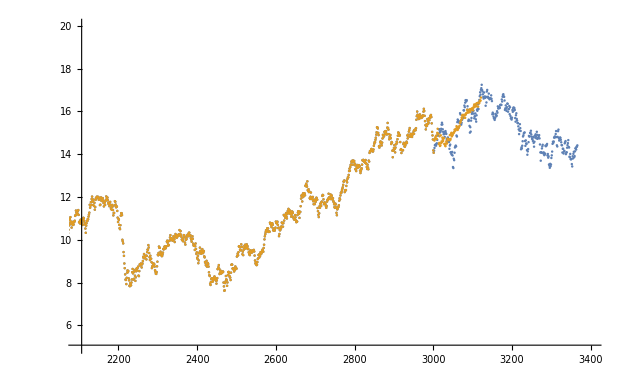

```mathematica
ListPlot[{FDClose[s[[1]]][[800;;,2]],csf[[1]]},PlotRange->{{2100,3400},{5,20}}]
```

```mathematica
PredictorInformation[csf[[2]],"Options"]
```

Missing[PropertyNotAvailable,Options]

```mathematica
pm=MPPredictions[csf[[2]],FDClose[s[[1]]][[3780;;,2]],20]
```

PredictorMeasurementsObject[…]

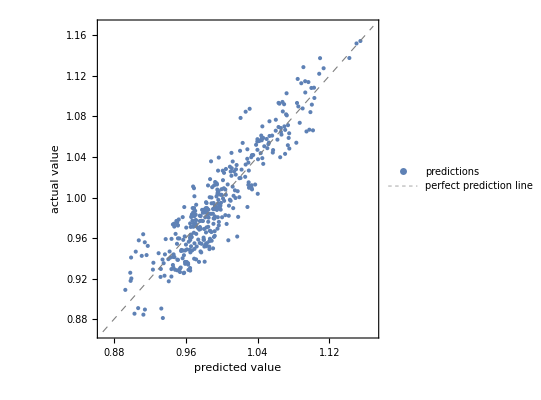
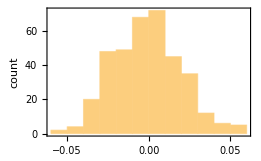
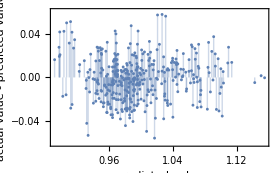
{-Graphics-,0.0163023,0.,-Graphics-,-Graphics-,{-0.0369345,-0.0323036,-0.0224467,-0.00194932,-0.0218844,0.00552622,-0.0121795,-0.000129385,0.0276835,0.0417664,0.0346457,0.0269224,0.0423769,0.0501343,0.0512428,0.0241263,0.0315991,-0.00149832,0.0118546,-0.0026207,0.0298763,0.0223835,0.0163092,-0.0222297,-0.0276431,-0.013148,0.000257145,0.00575305,-0.00579957,0.0155551,0.0066822,0.00379569,0.011273,-0.0126197,-0.020146,-0.0138938,0.0119617,-0.00491295,0.00545784,0.00842173,-0.0269249,-0.0152089,0.00473616,-0.0343827,-0.022638,-0.0127138,-0.0236475,-0.00248682,-0.00499923,-0.0421798,-0.0173674,0.0208271,0.0192885,0.0415295,0.0253869,0.0170733,0.0271459,-0.00409718,0.0426518,0.0156326,0.0562529,0.0578485,0.0573683,0.00841442,0.0304093,0.0103589,0.00535078,0.0374311,0.027727,-0.000328554,0.00161086,0.0132913,-0.0047776,0.0171476,-0.00520068,0.00924478,0.0216081,0.0321621,0.0264472,0.0281621,0.0123857,0.0176153,0.00730702,0.0101674,-0.0119193,-0.0255186,-0.00223343,-0.0236099,-0.0374616,-0.0208908,-0.017279,-0.0380493,-0.0557824,-0.0315829,-0.049573,-0.00656917,0.00615203,-0.00214856,0.0147874,0.0219024,0.0273126,0.00980279,0.00283534,-0.0139808,0.00415918,-0.015129,-0.012624,-0.0242748,-0.0113628,0.00617535,0.0153782,0.0255279,0.0218846,0.0247778,0.000205773,0.0154395,0.0303943,0.0136045,0.0133812,0.00711072,0.0169612,0.00560824,0.016703,-0.014727,-0.0133438,-0.0293863,-0.0271126,-0.00461814,-0.00241181,-0.0291909,-0.00646737,-0.0027986,-0.0257928,0.0105512,-0.000741981,0.0211677,0.0233913,-0.0131713,-0.0069272,-0.00557847,0.00718944,0.000818633,-0.0193991,0.00117127,-0.00534898,-0.00303085,0.00892961,-0.00239805,-0.008934,-0.0345435,-0.0284539,-0.0282546,-0.0115696,-0.016322,-0.0284503,-0.0101735,-0.0133888,-0.00661203,-0.0203865,-0.00688315,-0.0013527,0.0154831,-0.00286847,0.00661118,0.00159501,0.00268198,-0.00749019,-0.0022886,-0.00120131,0.00533618,0.00691098,-0.00368173,0.00463978,0.0137411,0.0030503,0.00614864,0.0025571,0.0134009,0.00149317,0.00758594,-0.0126564,-0.0365484,-0.0245202,-0.00195622,-0.0158647,-0.00715034,0.00782744,0.0207809,0.0203428,-0.0199595,0.00281301,-0.0108854,-0.00603333,-0.0217078,0.0165239,-0.0191704,-0.0246921,-0.0287504,-0.0273246,-0.00394726,0.0220725,0.0113013,0.0136102,0.00560597,0.00347288,0.0082714,-0.000917837,-0.0215562,-0.0372508,0.00594597,0.00962487,0.00250556,-0.0068775,-0.0167653,-0.0232837,-0.0260699,-0.0195738,-0.0307815,-0.0254145,0.0240727,-0.0074875,0.00718092,-0.053241,-0.0282639,-0.0249035,-0.0159729,0.016292,0.015357,0.0213754,0.0047897,0.0315389,0.0068525,-0.0119666,-0.0233605,-0.00908524,-0.0192518,-0.0204583,-0.0405272,-0.0321569,-0.0236523,0.0117492,-0.0037446,0.033062,0.0232027,0.0067914,0.00803678,0.0252449,0.03103,0.00257834,-0.00596805,-0.0110641,-0.0116071,-0.0193468,0.0176193,-0.0161514,-0.0233239,-0.00771852,0.0189031,-0.005099,0.0117674,0.00675507,-0.0212676,0.0180336,0.00954396,-0.000305212,-0.000532242,0.00588222,-0.00126232,0.00140619,-0.00450721,-0.0258554,-0.0314513,-0.0442958,-0.0204209,-0.00674592,-0.0018729,0.00382924,0.00327878,-0.0288727,-0.0296508,-0.0124181,-0.0295303,-0.01459,-0.00612892,0.0262103,0.0277947,0.00959423,0.00546222,0.0210968,-0.0313378,-0.00760119,-0.0214838,-0.0151007,-0.0275711,-0.0292699,-0.0382014,-0.0148331,-0.0342862,-0.0043889,0.0159313,0.0322675,0.0270878,0.0474803,0.0426147,0.0399951,0.0225559,0.0305145,0.0119334,0.0216547,0.00481099,-0.00408952,0.00435464,-0.00126628,-0.0355361,-0.0308299,0.00797198,0.0238936,0.0137983,-0.00893622,-0.0159382,0.000560282,-0.0105677,-0.00178197,-0.0116309,-0.0115856,-0.00165977,-0.020929,-0.029042,-0.00572756,-0.00254328,-0.0324814,-0.0246191,-0.00688959,0.00979909,0.0195559,0.0163924,-0.0193401,-0.00265506,-0.0148216,0.00982048,0.0157679,0.00649225,0.0212563,-0.000267844,-0.00118582,-0.0301129,-0.0302705,0.0127618,-0.0226492,-0.01696,0.0051734,-0.0153526,-0.0159506,0.00105027,-0.011473,0.0151179,0.0126649,-0.00626098,0.00401953,0.00738242,0.0203338,0.0120348,-0.00358121,0.00677708,0.00409813,0.00964134},0.0203559,0.151657}

```mathematica
pm/@{"ComparisonPlot","MeanDeviation","RejectionRate","ResidualHistogram","ResidualPlot","Residuals","StandardDeviation","TotalSquare"}
```

```mathematica
i=9;
```

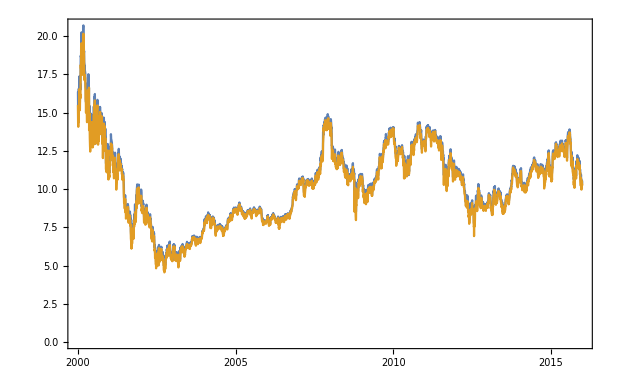

```mathematica
DateListPlot[{FDHigh[s[[i]]],FDLow[s[[i]]]}]
```

```mathematica
hs=FDHigh[s[[i]]][[;;2600,2]];
```

```mathematica
ls=FDLow[s[[i]]][[;;2600,2]];
```

```mathematica
ms=FDMedianPrice[s[[i]]][[;;2600,2]];
```

```mathematica
hsp=kNNForecast[hs,20,120,1];lsp=kNNForecast[ls,20,120,1];msp=kNNForecast[ms,20,120,1];
```

```mathematica
Length[hsp]
```

2720

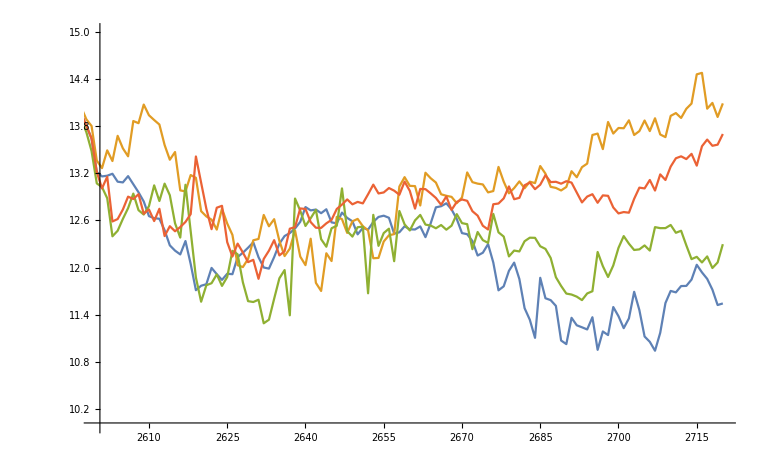

```mathematica
ListLinePlot[{FDMedianPrice[s[[i]]][[;;2720,2]],hsp,lsp,msp},PlotRange->{{2600,2720},{10,15}}]
```

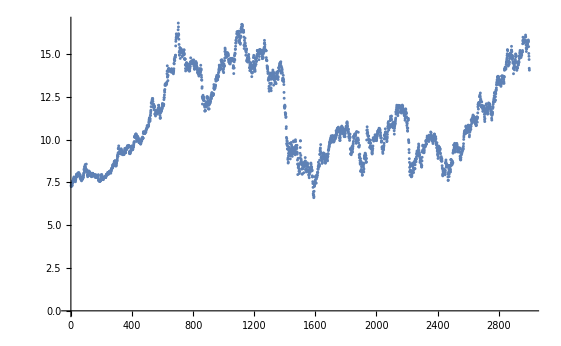

```mathematica
ListPlot[cs]
```

```mathematica
dev=emd[cs];
```

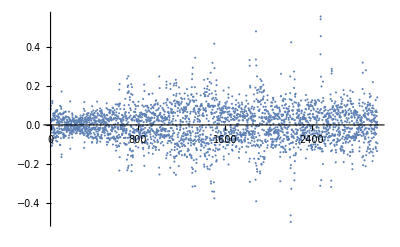
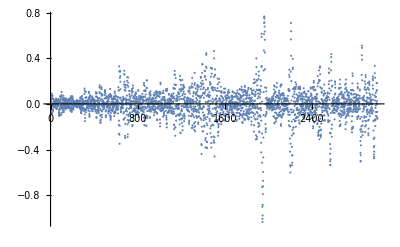
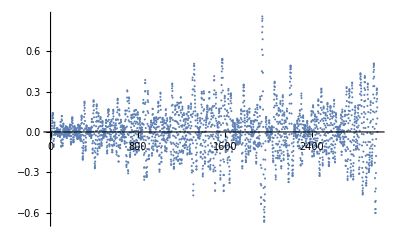
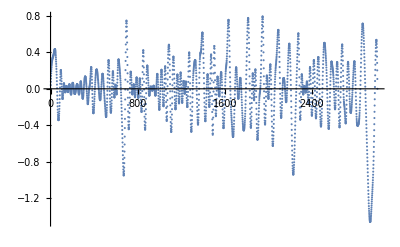
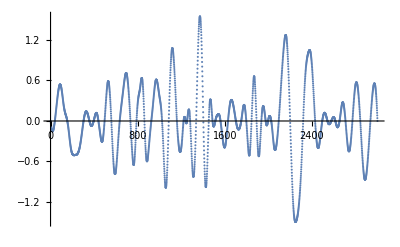
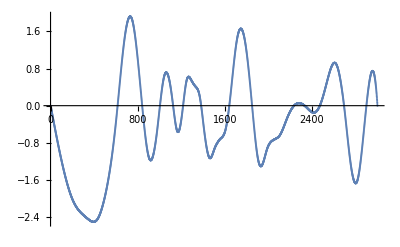
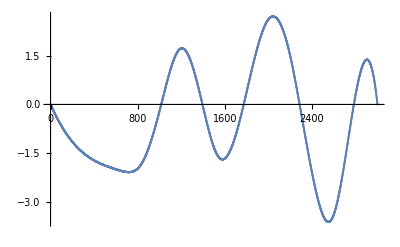
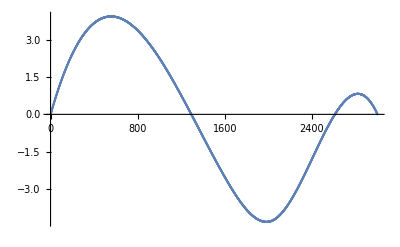

```mathematica
ListPlot[#,PlotRange->All]&/@dev
```

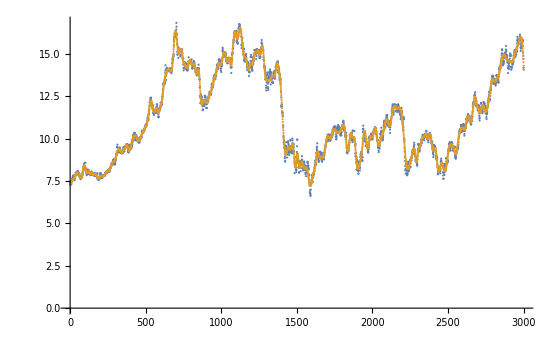

```mathematica
ListPlot[{cs,Plus@@dev[[-7;;]]},PlotRange->All]
```

```mathematica
pred=Table[Interpolation[dev[[i]],Method->"Spline"]/@Range[3001,3100],{i,1,10}];
```

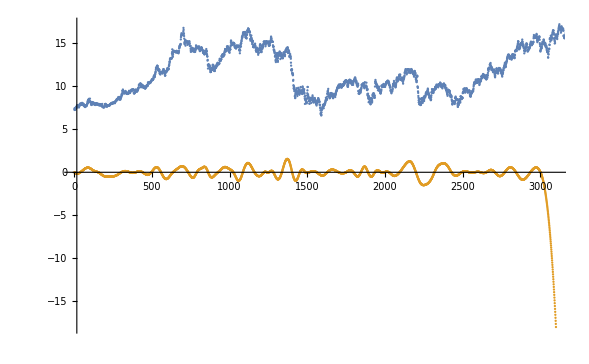

```mathematica
ListPlot[{FDClose[s[[1]]][[800;;,2]],Join[dev[[5]],pred[[5]]]},PlotRange->{{1,3100},All}]
```

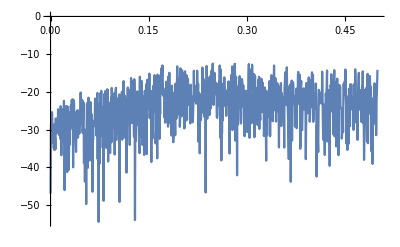

```mathematica
Periodogram[dev[[1]],PlotRange->All]
```

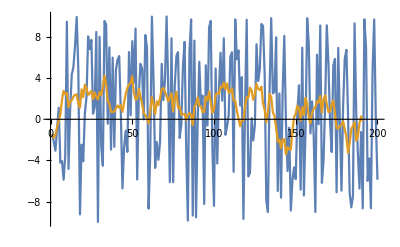

```mathematica
SeedRandom[42];
testData=RandomReal[{-10,10},{200}];
testsData=MovingAverage[testData,10];
ListLinePlot[{testData,testsData}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

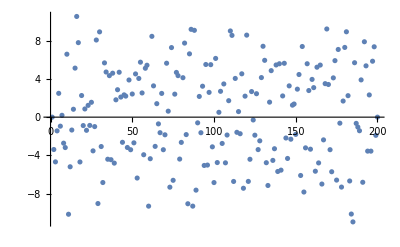
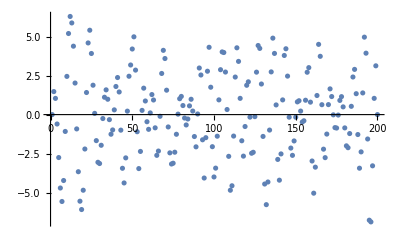
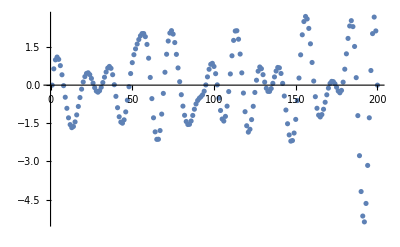
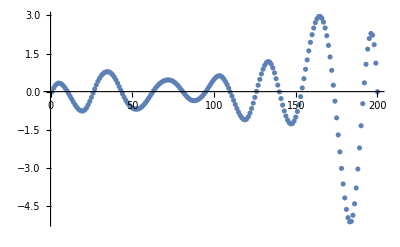
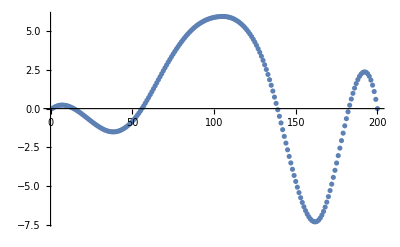
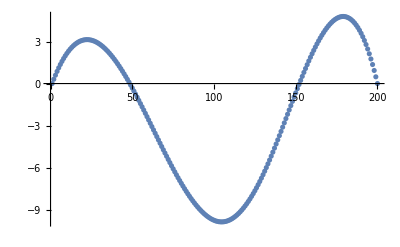
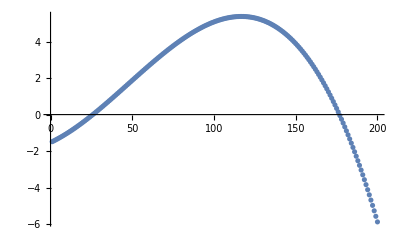

```mathematica
ListPlot[#,PlotRange->All]&/@emd[testData]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

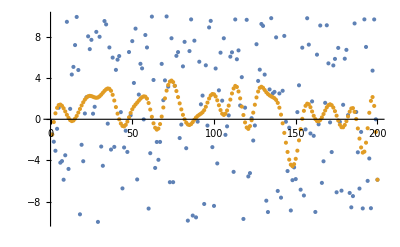

```mathematica
ListPlot[{testData,Plus@@emd[testData][[-5;;]]},PlotRange->All]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

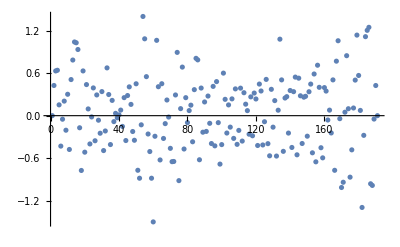
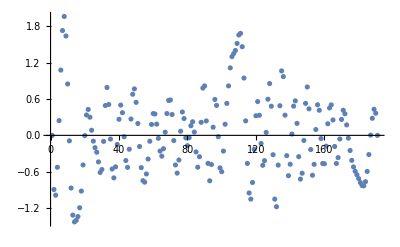
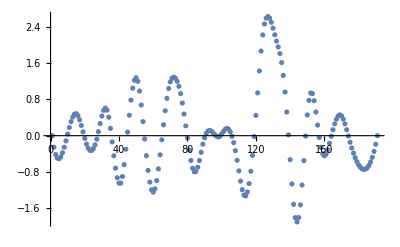
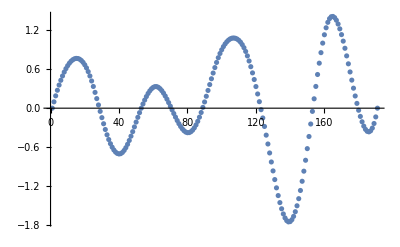
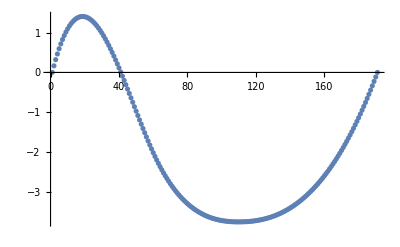
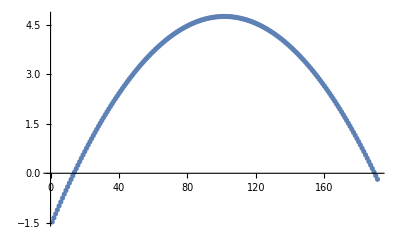

```mathematica
ListPlot[#,PlotRange->All]&/@emd[testsData]
```